```mathematica
v:=0.5;
f[t_]:=4*ArcTan[Exp[v*t/Sqrt[1-v^2]]]
```

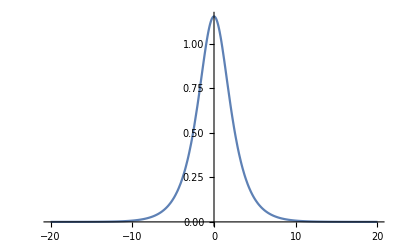

```mathematica
Plot[f'[t],{t,-20,20},PlotRange->All]
```

```mathematica
j[t_,a_,w_,nu_]:=NIntegrate[Exp[-nu*t1]*Sin[f[t-t1]+a*Sin[w*(t-t1)]-f[t]-a*Sin[w*t]],{t1,0,Infinity},PrecisionGoal->12,MaxRecursion->100]
j1[t_,a_,w_,nu_]:=BesselJ[0,a]^2*NIntegrate[Exp[-nu*t1]*Sin[f[t-t1]-f[t]],{t1,0,Infinity},PrecisionGoal->12,MaxRecursion->40]
```

```mathematica
j[3,0.1,10,0.5]//AbsoluteTiming
j1[3,0.1,10,0.5]//AbsoluteTiming
```

{0.0258223,-0.516967}

{0.0099015,-0.594765}

```mathematica
l=Table[j[t,1,10,0.5],{t,0,20,0.1}];//AbsoluteTiming
ll=Table[j1[t,1,10,0.5],{t,0,20,0.1}];//AbsoluteTiming
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{9.15596,Null}

{1.57292,Null}

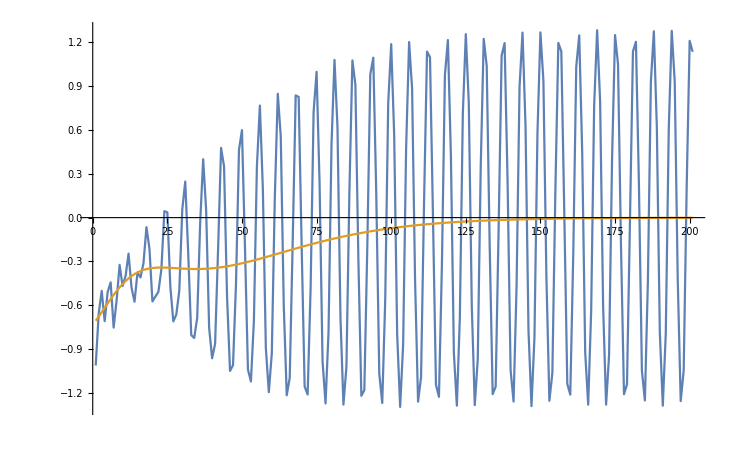

```mathematica
ListLinePlot[{l,ll},PlotRange->Full]
```